```mathematica
Remove["Global`*"]
```

Given a nonlinear second order differential equation, d^2x/dt^2 = x^2 - x that can be thought of as Newton’s second law for x(t) of a particle moving in one dimension, i try solving the equation using Dsolve function but it doesn’t work because this function can only be solved numerically

```mathematica
solm = DSolve[{x''[t]==(x[t]^2) -x[t], x[0]== 0, x'[0] == 0}, x[t], t];
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

Now i try again to solve it using the NDSolve function which solves numerically

```mathematica
sola = NDSolve[{x''[t]==(x[t]^2) -x[t], x[0]==0, x'[0]==0}, x[t], {t, 0, 10}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
b= x[t]/.sola
```

{InterpolatingFunction[…][t]}

I then plot my resulting numerical answer and its just a line at 0

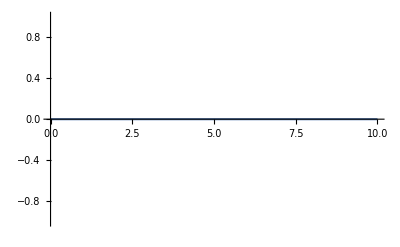

```mathematica
Plot[b, {t,0,10}]
```

I adjusted the boundary conditions to get two new functions with x(0)=0.1 and x(0)=-0.1

```mathematica
sol1 = NDSolve[{x''[t]==(x[t]^2) -x[t], x[0]==0.1, x'[0]==0}, x[t], {t, 0, 10}]
b1 = x[t] /. sol1
sol2 = NDSolve[{x''[t]==(x[t]^2) -x[t], x[0]==-0.1, x'[0]==0}, x[t], {t, 0, 10}]
b2 = x[t]/.sol2
```

{{x[t]→InterpolatingFunction[…][t]}}

{InterpolatingFunction[…][t]}

{{x[t]→InterpolatingFunction[…][t]}}

{InterpolatingFunction[…][t]}

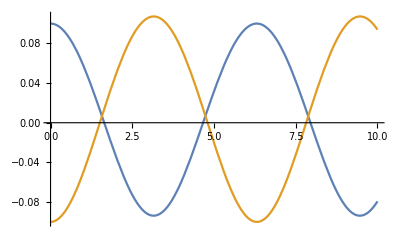

```mathematica
Plot[{b1,b2}, {t, 0,10}]
```

The resulting graph from the two new boundary conditions resembles a cos function and an inverse cos function. considering that the main difference is a negative sign on the boundary condition, this tells me that the boundary condition can have a significant effect on the motion of the graph. I now try new boundary conditions to get new functions and check the resulting graph

```mathematica
sol3 = NDSolve[{x''[t]==(x[t]^2) -x[t], x[0]==0.5, x'[0]==0}, x[t], {t, 0, 10}]
b3 = x[t]/.sol3
sol4 = NDSolve[{x''[t]==(x[t]^2) -x[t], x[0]==-0.5, x'[0]==0}, x[t], {t, 0, 10}]
b4 = x[t]/.sol4
```

{{x[t]→InterpolatingFunction[…][t]}}

{InterpolatingFunction[…][t]}

{{x[t]→InterpolatingFunction[…][t]}}

{InterpolatingFunction[…][t]}

The resulting graph of the new boundary conditions of x(0)=0.5 and x(0)=-0.5 shows one line seemingly constant at 0 and another dropping to negative infinity at 12 or 13

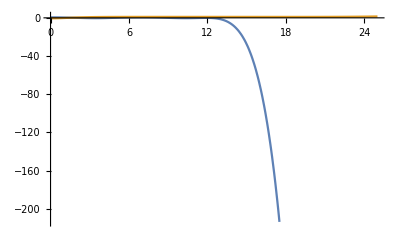

```mathematica
Plot[{b3, b4}, {t,0,25}]
```

I now only check for the motion with x(0)=-0.51 and adjust the plot range to get a graph that seems to have an error at some 8 or 9 value

NDSolve::ndsz: At t == 9.13172, step size is effectively zero; singularity or stiff system suspected.

{{x[t]→InterpolatingFunction[…][t]}}

{InterpolatingFunction[…][t]}

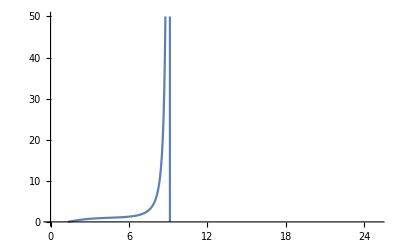

```mathematica
sol5 = NDSolve[{x''[t]==(x[t]^2) -x[t], x[0]==-0.51, x'[0]==0}, x[t], {t, 0, 10}]
b5 = x[t]/.sol5
Plot[b5, {t, 0, 25}, PlotRange->{0,50}]
```

InterpolatingFunction::dmval: Input value {-24.999} lies outside the range of data in the interpolating function. Extrapolation will be used.

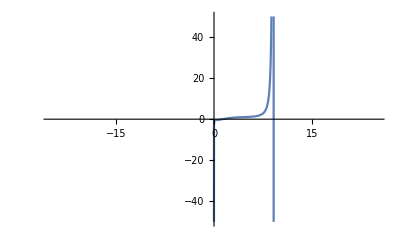

```mathematica
Plot[b5, {t, -25, 25}, PlotRange->{-50,50}]
```

```mathematica
sol6 = NDSolve[{x''[t]==(x[t]^2) -x[t], x[0]==-0.51, x'[0]==0}, x[t], {t, -8, 8}]
b6 = x[t]/.sol6
```

{{x[t]→InterpolatingFunction[…][t]}}

{InterpolatingFunction[…][t]}

I then adjust the boundary conditions for solving the differential equation and plotting the function one more time

InterpolatingFunction::dmval: Input value {-24.999} lies outside the range of data in the interpolating function. Extrapolation will be used.

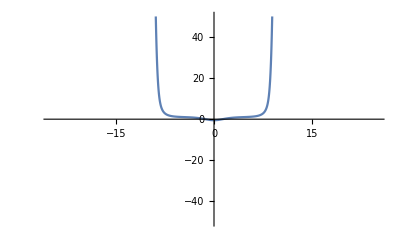

```mathematica
Plot[b6, {t, -25,25}, PlotRange->{-50,50}]
```

The resulting graph shows the motion with the -0.51 boundary condition .

```mathematica
?Integrate
```

```mathematica
p=-Integrate[x^2-x,x]
```

x^2/2-x^3/3

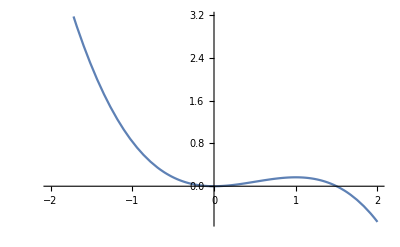

```mathematica
Plot[p,{x,-2,2}]
```

The plot for potential energy shows how at around 0.5 the potential energy goes to zero which means the energy is converted from potential energy to kinetic energy. for a mass traveling down a hill with set potential energy, at 0.5 the potential energy of the mass would get converted to kinetic energy and the mass would continue travelling which isn’t shown in the graph.